## Kapitola 9 - Shlukování dat sítí bez učitele

Demonstrace použití neuronové sítě bez učitele k hledání shluků v datech.

## Inicializace knihovny NeuralNetworks

Nejprve načteme knihovnu pro neuronové sítě.

```mathematica
<<NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm];
```

## Vytvoření trénovacích dat

Vygenerujeme si data, na kterých budeme prezentovat shlukování. Protože pracujeme se sítí bez učitele, postačí nám vstupní data a nepotřebujeme generovat žádná výstupní data.

```mathematica
values=10;
cluster1x =RandomReal[{-0.1,0.1},{values,1}];cluster1y=RandomReal[ {-0.1,0.1},{values,1}];
cluster2x =RandomReal[{-0.1,0.1},{values,1}];cluster2y=RandomReal[ {0.9,1.1},{values,1}];
cluster3x =RandomReal[{0.3,0.5},{values,1}];cluster3y=RandomReal[ {1.4,1.6},{values,1}];
cluster4x =RandomReal[{0.9,1.1},{values,1}];cluster4y=RandomReal[ {2.1,1.9},{values,1}];
cluster5x =RandomReal[{1.4,1.6},{values,1}];cluster5y=RandomReal[ {1.4,1.6},{values,1}];
cluster6x =RandomReal[{1.9,2.1},{values,1}];cluster6y=RandomReal[ {1.1,0.9},{values,1}];
cluster1=Join[cluster1x,cluster1y,2];
cluster2=Join[cluster2x,cluster2y,2];
cluster3=Join[cluster3x,cluster3y,2];
cluster4=Join[cluster4x,cluster4y,2];
cluster5=Join[cluster5x,cluster5y,2];
cluster6=Join[cluster6x,cluster6y,2];
inData= Join[cluster1,cluster2,cluster3,cluster4,cluster5,cluster6];
```

Vygenerovaná data jsou dvoudimenzionální a obsahují 6 jasně oddělených shluků.

Data si můžeme zobrazit zde.

```mathematica
inData
```

{{0.0237858,0.0446933},{-0.0798236,-0.0855344},{-0.0542112,0.0224457},{0.0319375,0.0231101},{-0.0487605,0.0377006},{0.0269231,0.0301954},{-0.0612284,-0.0211725},{0.0400639,0.0459256},{0.0249398,-0.0982167},{-0.0218302,-0.00687589},{0.0586566,0.921764},{-0.0561961,1.05162},{0.0673423,1.05358},{-0.0595621,0.949413},{0.0170599,1.04541},{0.0717458,1.02595},{-0.0869371,0.941721},{0.00652862,1.06369},{0.0617104,1.07484},{0.0310509,1.09202},{0.328388,1.47527},{0.471944,1.47566},{0.403615,1.59531},{0.386184,1.44312},{0.336141,1.58439},{0.328492,1.4778},{0.397263,1.51772},{0.497231,1.56624},{0.388724,1.56927},{0.461784,1.43219},{1.08841,2.08917},{0.901373,1.99426},{0.920954,1.94859},{1.06572,2.05801},{0.992526,2.06983},{1.02364,2.00254},{0.999137,1.91886},{0.976896,2.03371},{1.02918,2.06615},{1.05897,2.0644},{1.40143,1.58015},{1.42673,1.4851},{1.5817,1.51535},{1.54665,1.45066},{1.4242,1.41097},{1.40162,1.43612},{1.48296,1.52807},{1.45361,1.43363},{1.5691,1.57569},{1.40055,1.40426},{1.93956,0.955863},{1.97494,0.957568},{1.98766,1.02329},{2.01572,0.981412},{2.03977,1.02365},{2.00499,1.09656},{2.08442,0.971841},{1.97828,0.923921},{2.02189,1.04299},{1.97195,1.07371}}

Pro lepší představu o struktuře dat si je můžeme zobrazit v grafu.

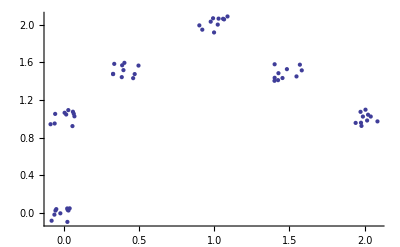

```mathematica
ListPlot[inData]
```

## Zpracování dat neuronovou sítí

### Náhodně inicializovaná síť

Nejprve vytvoříme neuronovou síť o šesti neuronech. Počet neuronů určuje kolik shluků se síť pokusí v datech najít.

```mathematica
unsup=InitializeUnsupervisedNet[inData,6];
```

Tuto neuronovou síť naučíme na našich datech

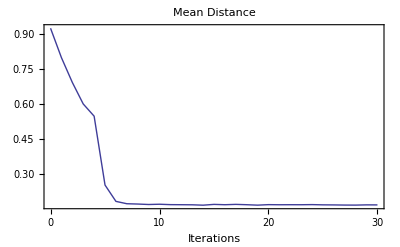

UnsupervisedNet::DeadNeuron: Some codebook vectors are not used by the data. They have 'died' during the training. Use UnUsedNeurons to identify them and decide if you want to remove them.

```mathematica
{unsup,fitrecord}=UnsupervisedNetFit[inData,unsup,30,ReportFrequency->1];
```

Vidíme že během učení sítě jeden z neuronů “zemřel”, tzn. není použit k rozlišení shluků v datech. Později se mu ještě budeme věnovat.

Ilustraci jaým způsobem byla data rozdělena do shluků nám poskytne následující graf. Pozice neuronu, který reprezentuje daný shluk je naznačena tučným číslem. Je také jasně vidět, který neuron je “mrtvý” a nepřináší nám žádný užitek.

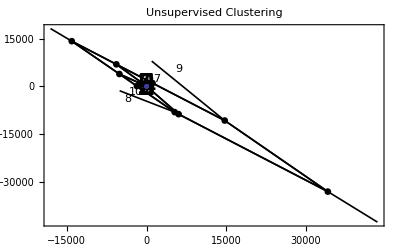

```mathematica
NetPlot[unsup,inData,CbvSymbol->{FontSize->30}]
```

Můžeme také jednoduše nechat “oklasifikovat” nový vektor (zadáme jeho x a y souřadnici).

```mathematica
unsup[{0.2,0.7}]
```

{3}

Číslo, které nám síť vrátila znamená číselné označení shluku, kam vektor spadá (odpovídá číslům v grafu)

Nyní si vzpomeneme, že máme v síti nepotřebný neuron, budeme ho tedy chtít odstranit.
Nejdříve zjistíme o který neuron se jedná.

```mathematica
UnUsedNeurons[unsup,inData]
```

{6}

A poté ho odstraníme. Novou síť bez nepotřebného neuronu pojmenujeme unsup1.

```mathematica
unsup1=NeuronDelete[unsup,%]
```

UnsupervisedNet[{-Codebook Vectors-},{CreationDate → {2011, 4, 5, 20, 51, 53.079799}, AccumulatedIterations → 30, SOM → None}]

Podíváme se jakým způsobem odděluje síť jednotlivé shluky po odebrání nepotřebného neuronu.

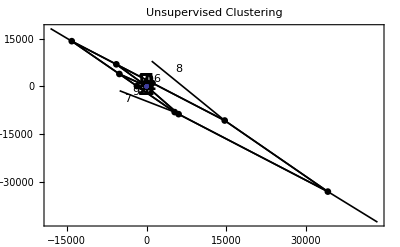

```mathematica
NetPlot[unsup1,inData,CbvSymbol->{FontSize->30}]
```

### Síť inicializovaná metodou SOM

Protože vidíme, že rozdělení dat na shluky ještě není perfektní můžeme se pokust dosáhnout ještě lepšího rozdělení. Místo náhodné inicializace sítě můžeme použít SOM (samoorganizující mapu) k inicializaci sítě. Samoorganizující mapa se nechá přizpůsobit datům, na souřadnicích, kde skončí její neurony, jsou inicializovány neurony naší požadované sítě (naše síť není SOM).

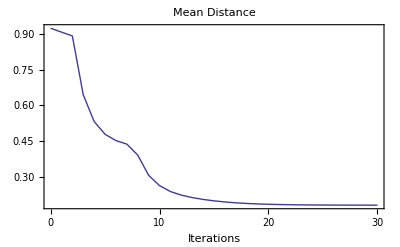

```mathematica
unsup2=InitializeUnsupervisedNet[inData,6,UseSOM ->True,CriterionPlot->True,CriterionLog->True,Iterations->30];
```

Nyní naučíme zinicializovanou síť na našich datech.

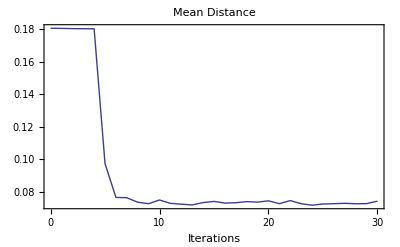

```mathematica
{unsup2,fitrecord2}=UnsupervisedNetFit[inData,unsup2,30];
```

A podíváme se jakým způsobem uřčuje shluky v datech.

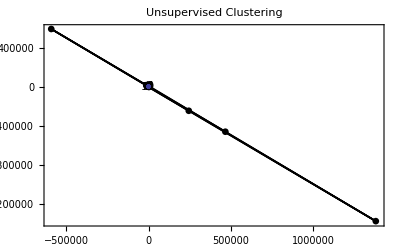

```mathematica
NetPlot[unsup2,inData]
```

Tento přístup k inicializaci sítě nám může často pomoci dosáhnout lepších výsledků, než náhodná inicializace. Také často zabrání problému s “mrtvými” neurony.

## Průběh učení

### Náhodně inicializovaná síť

Ještě se můžeme podívat jak síť v průběhu učení dělila data do shluků a jak se měnila poloha jednotlivých neuronů. Barevné čáry ukazují pohyb jednotlivých neuronů, čísla ukazují jejich konečnou polohu.

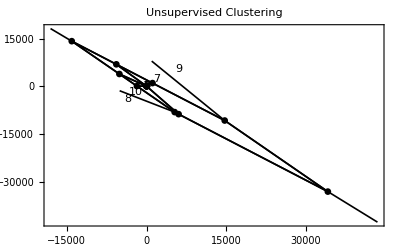

```mathematica
NetPlot[fitrecord,inData]
```

Zde si můžete zobrazit průběh učení po jednotlivých iteracích.

```mathematica
learningState=NetPlot[fitrecord,inData,DataFormat->DataMapArray,Intervals->1][[1,2,All,1,1]];
Manipulate[learningState[[a]],{{a,1, "Iteration"}, 1, 31,1}]
```

### Síť inicializovaná metodou SOM

Z následujícího grafu je patrné, že i pouze zinicializovaná síť metodou SOM by poskytovala poměrně dobré výsledky a její učení upravuje pouze pozici několika neuronů.

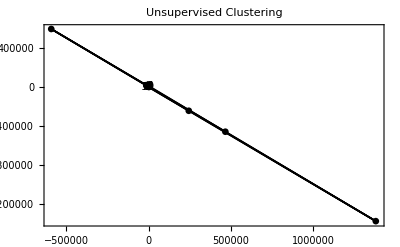

```mathematica
NetPlot[fitrecord2,inData]
```

Zde si můžete zobrazit průběh učení po jednotlivých iteracích.

```mathematica
learningState2=NetPlot[fitrecord2,inData,DataFormat->DataMapArray,Intervals->1][[1,2,All,1,1]];
Manipulate[learningState2[[a]],{{a,1, "Iteration"}, 1, 31,1}]
```

## Prohlášení

Tento text je součástí bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011.